# Integrali

Tit Arnšek;

Praktična Matematika, UL FMF;
ROM;
1. letnik

## Definicija integrala

Integral je osnova matematične analize in infinitezimalnega računa. Temelje integralskega računa sta postavila Isaac Newton in Gottfried Wilhelm Leibniz v poznem 17. stoletju. Integral funkcije je prek osnovnega izreka infinitezimalnega računa povezan z njenim odvodom, določen integral funkcije na nekem intervalu pa je, ko poznamo nedoločenega, povsem enostavno izračunati. Gre za orodje, ki je  izjemno uporabno v znanosti in tehniki. Integral označimo z znakom ∫.
Beseda integral zajema dva precej različna pojma:

Nedoločeni integral in

Določeni integral

## Nedoločeni integral

Nedoločeni integral dane funkcije 𝒻 je družina funkcij ℱ, katerih odvod je enak dani funkciji 𝒻. V tem smislu je integriranje inverzna operacija kot odvajanje. Rezultat nedoločenega integrala imenujemo primitivna funkcija.

### Nekaj primerov nedoločenega integrala:

V naslednjih primerih bom izračunal nekaj osnovnih nedoločenih integralov. Računamo jih s funkcijo Integrate.

∫ x^ndx

```mathematica
Integrate[x^n,x]
```

x^(1+n)/(1+n)

∫ 1/x dx

```mathematica
Integrate[1/x,x]
```

Log[x]

∫ Sin[x]dx

```mathematica
Integrate[Sin[x],x]
```

-Cos[x]

∫ Cos[x]dx

```mathematica
Integrate[Cos[x],x]
```

Sin[x]

∫ 1/Cos[x]^2 dx

```mathematica
Integrate[1/Cos[x]^2,x]
```

Tan[x]

∫ 1/Sin[x]^2 dx

```mathematica
Integrate[1/Sin[x]^2,x]
```

-Cot[x]

∫ ⅇ^x dx

```mathematica
Integrate[E^x,x]
```

ⅇ^x

∫ 1/(x^2+1)dx

```mathematica
Integrate[1/(x^2+1),x]
```

ArcTan[x]

## Določeni integral

Določeni integral je povezan s ploščino lika, omejenega z grafom funkcije 𝒻. Naj bosta dana pozitivna funkcija f realne spremenljivke x in interval [a, b] na številski premici. Določeni integral funkcije 𝒻 je ploščina lika, ki ga omejujejo graf funkcije 𝒻, os x ter navpični premici x = a in  x = b.

### Nekaj primerov računanja z določenim integralom:

Določene integrale računamo enako kot nedoločene, le da tukaj dodamo zraven še meje. Kadar integral aproksimira k neki vrednosti, ki je ne moremo “natančno” napisati, uporabimo funkcijo NIntegrate, ki nam vrne približek. 
Primeri:

Izračunaj integral ∫_0^1 1/(x^3+1)dx

```mathematica
Integrate[1/(x^3+1),{x,0,1}]
NIntegrate[1/(x^3+1),{x,0,1}]
```

1/18 (2 √3 π+Log[64])

0.835649

Izračunaj integral ∫_0^1 1/x Cos[Log[x]/x]dx

0.323367

∫_0^1 Cos[Log[x]/x]/x ⅆx

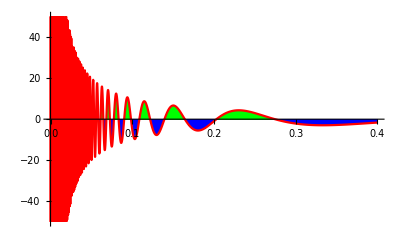

```mathematica
NIntegrate[1/x Cos[Log[x]/x],{x,0,1}]
Integrate[1/x Cos[Log[x]/x],{x,0,1}]
Plot[1/x  Cos[Log[x]/x],{x,0,0.4},PlotRange->50,PlotStyle->{Red},Filling->Axis, FillingStyle->{Blue,Green}]
```

Izračunaj integral ∫_0^(2π) x^2 Sin[2x]dx

-2 π^2

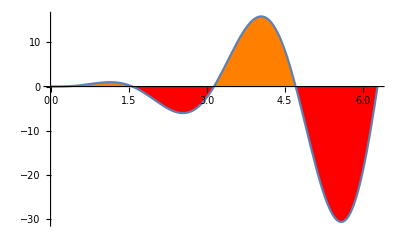

```mathematica
Integrate[x^2 Sin[2 x],{x,0,2 π}]
Plot[x^2 Sin[2 x],{x,0,2 π},Filling->Axis, FillingStyle->{Red,Orange}]
```

Opomba: 
Določeni integral lahko pride tudi negativen!

Računamo lahko tudi integrale z mejami v “neskončnosti”

Izračunaj integral ∫_ⅇ^∞ dx/(x^2 Log[x])

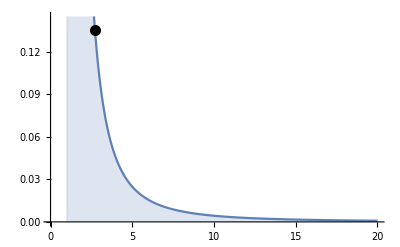

0.219384

```mathematica
Plot[1/(x^2*Log[x]),{x,0,20},PlotRange->{0,0.145},Filling->Axis  ,Epilog->{PointSize[0.02],,Point[{E,1/(E^2*Log[E])}]}]
NIntegrate[1/(x^2*Log[x]),{x,E,Infinity}]
```

Integral je lahko enak 0, v primeru, da je ploščina lika pod abscisno osjo enaka ploščini nad abscisno osjo.

Preučuj določeni integral od funkcjije Sin[x].

```mathematica
ClearAll[g,x]
g[x_]:= Sin[x] 
a = Manipulate[{Show[{Plot[g[x],{x,0,4Pi},Filling->Axis, FillingStyle->{Red,Orange},GridLines->{{n,0},{5,0}}, GridLinesStyle->Directive[Green,Thick, Dashed],
               Epilog->{PointSize[0.03],Point[{n,g[n]}] }]
                }],
		    Integrate[g[x],{x,0,n}]}, {n,0,4Pi}]
```

Opomba: 
Gledal sem določeni integral od 0 do n. Vidimo, da je določeni integral na vsakih 2kπ, k ∈ ℤ enak 0. To je zato, ker imajo “hribčki” in “doline” enako ploščino.

Preučuj določeni integral od funkcjije f[x] = |Sin[x] - 0.5|.

```mathematica
f[x_]:= Abs[Sin[x] - 0.5]
Manipulate[{Show[{Plot[f[x],{x,0,5Pi},Filling->Axis,GridLines->{{n,0},{0,0}},GridLinesStyle->Directive[Green,Thick, Dashed],
               Epilog->{PointSize[0.03],Point[{n,f[n]}] }]
                }],Integrate[f[x],{x,0,n}]},{n,0,5Pi}]
```

Opomba:
Ker je graf te funkcije vedno nad abscisno osjo, integral vedno narašča.

### Kaj lahko počnemo z določenim integralom?

S pomočjo določenega integrala lahko izračunamo stvari kot so: ploščina lika med grafom krivulje in abscisno osjo, ploščino lika dveh funkcij, volumen vrtenine, dolžino krivulje na intervalu, za določanje središč ravninskih likov, površino vrtenine in še za veliko drugih stvari. Nekatere izmed teh bom predstavil.

#### Ploščina lika med grafom krivulje in abscisno osjo

Zelo pogosta uporaba določenega intervala pri matematiki je pri računanju ploščine lika, ki je omejen z grafom krivulje in abscisno osjo. To naredimo tako, da izračunamo določeni integral te funkcije, ki ima za meji točki, med katerima nas zanima ploščina. Če je graf krivulje pod abscisno osjo, potem moramo vzeti absolutno vrednost od dobljene vrednosti, saj je določeni integral v tem primeru negativen.

Primer:
Izračunaj ploščino lika med krivuljo y = x^2 - 4  in abscisno osjo.

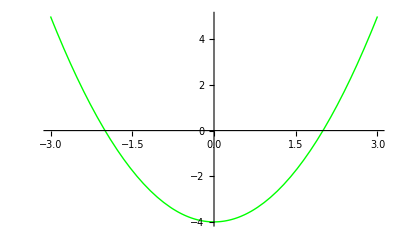

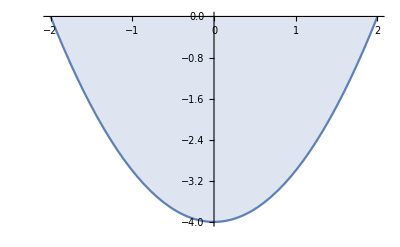

{{x→-2},{x→2}}

32/3

```mathematica
ClearAll[x,f]
f[x_]:=x^2-4
Plot[f[x],{x,-3,3},PlotStyle->{Green,Thick}]
Plot[f[x],{x,-2,2},Filling->Axis]
ničle = Solve[f[x]==0,x]
ploščina = -Integrate[f[x],{x,-2,2}]
```

Ploščina grafa med grafom funkcije in abscisno osjo je 32/3.

#### Ploščina lika dveh funkcij

Pri računanju ploščine lika med dvama krivuljema je formula zelo podobna prejšnji. Gre za enako formulo, saj je prejšnji primer posebni primer te formule. Pri tej formuli prav tako izračunamo določeni integral od razlike zgornje in spodnje krivulje, ki dani lik omejujeta. Formula se glasi:  pl = ∫_a^b |f[x]-g[x]|ⅆx, kjer je f[x] zgornja krivulja, g[x] pa spodnja.

Primer:
Izračunaj ploščino lika, ki ga omejujeta krivulji y=x^2-4x-2 in y=-x^2+4.

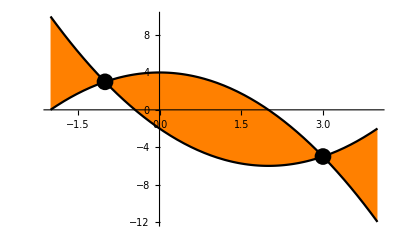

{{x→-1},{x→3}}

64/3

```mathematica
ClearAll[f,x]
f[x_]:=x^2-4x-2
g[x_]:=-x^2+4
Plot[{f[x],g[x]},{x,-2,4}, PlotStyle->Black,Filling->{1->{2}},FillingStyle->Orange,Epilog->{PointSize[0.03],Point[{-1,f[-1]}],Point[{3,f[3]}]}]
presečišča = Solve[f[x]==g[x],x]
ploščina = Integrate[Abs[f[x]-g[x]],{x,-1,3}]
```

Ploščina grafa med grafom funkcij  je 64/3.

#### Volumen vrtenine

Volumen vrtenine, ki jo dobimo tako, da krivuljo neke funkcije zavrtimo okoli abscisne osi, dobimo po enačbi: V = π∫_a^b f[x]^2 ⅆx.

Primer: 
Dana je funkcija f[x]=2/x. Del grafa, ki pripada intervalu x∈[1,4], zavrtimo za 360∘ okoli abscisne osi. Izračunaj prostornino tako dobljene vrtenine.

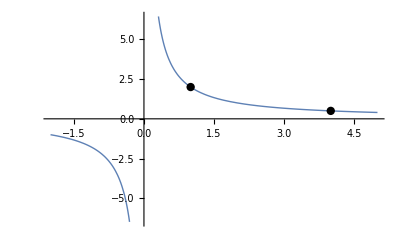

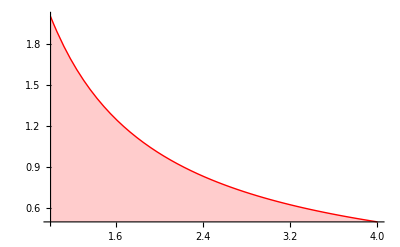

3 π

```mathematica
h[x_]= 2/x;
Plot[h[x],{x,-2,5}, PlotStyle->Thick,Epilog->{PointSize[0.015],Point[{1,h[1]}],Point[{4,h[4]}]}]
Plot[2/x,{x,1,4},Filling->Axis,PlotStyle->Directive[Red,Thick]]
meja1 = 1;
meja2 = 4;
volumen = Pi*Integrate[h[x]^2,{x,meja1,meja2}]
```

Volumen vrtenine je 3π.

#### Dolžina krivulje na intervalu

Za izračun dolžine krivulje na intervalu [a,b], uporabimo formulo: ℓ = ∫_a^b √(1+f'[x]^2)ⅆx.

Primer: 
Dana je funkcija f[x] =x^2/8-Log[x]. Izračunaj dolžino krivulje te funckije na intervalu [1,2].

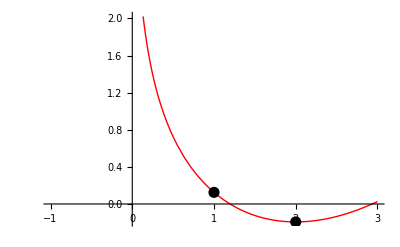

x (x^2/8-Log[x])

1.02535

```mathematica
ClearAll[f,x]
f[x_]:= x^2/8 - Log[x]
Plot[f[x],{x,-1,3},Epilog->{PointSize[0.02],Point[{1,f[1]}],Point[{2,f[2]}]},PlotStyle->Directive[Red,Thick]]
odvod = D[f[x]x]
dolžina = NIntegrate[Sqrt[1+odvod^2],{x,1,2}]
```

Dolžina krivulje med točakama x = 1 in x  = 2  je 1.02535.